### Parte 1 (Baterias de 1 a 5)

```mathematica
v1= .5;
```

```mathematica
bat1=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt1\\BAT1.xls"];
d1=13.16;
h1=30.83;
fTAV1=Table[{bat1[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d1^2 (* A[mm^2]*),v1 (* v[mm/s] *)},{i,1,Length[bat1]}];
deltaSt1=Table[{fTAV1[[i]][[2]]fTAV1[[i]][[4]],fTAV1[[i]][[1]]/fTAV1[[i]][[3]]},{i,1,Length[bat1]}];
strainStress1=Table[{deltaSt1[[i]][[1]]/h1,deltaSt1[[i]][[2]]},{i,1,Length[bat1]}];
strainStressFit1=Table[{deltaSt1[[i]][[1]]/h1,deltaSt1[[i]][[2]]},{i,80,200}];
g1=ListPlot[strainStress1,PlotStyle->{Red,PointSize[.005]}];
```

```mathematica
bat2=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt1\\BAT2.xls"];
d2=12.89;
h2=31.34;
fTAV2=Table[{bat2[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d2^2 (* A[mm^2]*),v1 (* v[mm/s] *)},{i,1,Length[bat2]}];
deltaSt2=Table[{fTAV2[[i]][[2]]fTAV2[[i]][[4]],fTAV2[[i]][[1]]/fTAV2[[i]][[3]]},{i,1,Length[bat2]}];
strainStress2=Table[{deltaSt2[[i]][[1]]/h2,deltaSt2[[i]][[2]]},{i,1,Length[bat2]}];
strainStressFit2=Table[{deltaSt2[[i]][[1]]/h2,deltaSt2[[i]][[2]]},{i,100,200}];
g2=ListPlot[strainStress2,PlotStyle->{Purple,PointSize[.005]}];
```

```mathematica
bat3=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt1\\BAT3.xls"];
d3=13.2;
h3=30.84;
fTAV3=Table[{bat3[[i]][[1]]9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d3^2 (* A[mm^2]*),v1 (* v[mm/s] *)},{i,1,Length[bat3]}];
deltaSt3=Table[{fTAV3[[i]][[2]]fTAV3[[i]][[4]],fTAV3[[i]][[1]]/fTAV3[[i]][[3]]},{i,1,Length[bat3]}];
strainStress3=Table[{deltaSt3[[i]][[1]]/h3,deltaSt3[[i]][[2]]},{i,1,Length[bat3]}];
strainStressFit3=Table[{deltaSt3[[i]][[1]]/h3,deltaSt3[[i]][[2]]},{i,100,200}];
g3=ListPlot[strainStress3,PlotStyle->{Blue,PointSize[.005]}];
```

```mathematica
bat4=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt1\\BAT4.xls"];
d4=13.25;
h4=31.8;
fTAV4=Table[{bat4[[i]][[1]]9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d4^2 (* A[mm^2]*),v1 (* v[mm/s] *)},{i,1,Length[bat4]}];
deltaSt4=Table[{fTAV4[[i]][[2]]fTAV4[[i]][[4]],fTAV4[[i]][[1]]/fTAV4[[i]][[3]]},{i,1,Length[bat4]}];
strainStress4=Table[{deltaSt4[[i]][[1]]/h4,deltaSt4[[i]][[2]]},{i,1,Length[bat4]}];
strainStressFit4=Table[{deltaSt4[[i]][[1]]/h4,deltaSt4[[i]][[2]]},{i,100,200}];
g4=ListPlot[strainStress4,PlotStyle->{Orange,PointSize[.005]}];
```

```mathematica
bat5=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt1\\BAT5.xls"];
d5=13.2;
h5=30.84;
fTAV5=Table[{bat5[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d5^2 (* A[mm^2]*),v1 (* v[mm/s] *)},{i,1,Length[bat5]}];
deltaSt5=Table[{fTAV5[[i]][[2]]fTAV5[[i]][[4]],fTAV5[[i]][[1]]/fTAV5[[i]][[3]]},{i,1,Length[bat5]}];
strainStress5=Table[{deltaSt5[[i]][[1]]/h5,deltaSt5[[i]][[2]]},{i,1,Length[bat5]}];
strainStressFit5=Table[{deltaSt5[[i]][[1]]/h5,deltaSt5[[i]][[2]]},{i,100,200}];
g5=ListPlot[strainStress5,PlotStyle->{Magenta,PointSize[.005]}];
```

```mathematica
pointsSet1=Join[strainStressFit1,strainStressFit2,strainStressFit3,strainStressFit4,strainStressFit5];
line1=Fit[pointsSet1, {1,x},x] (* Daqui tiramos que E = 3.22 MPa*)
```

-0.321001+3.21877 x

```mathematica
dP1=StandardDeviation[pointsSet1]
```

{0.04963,0.197507}

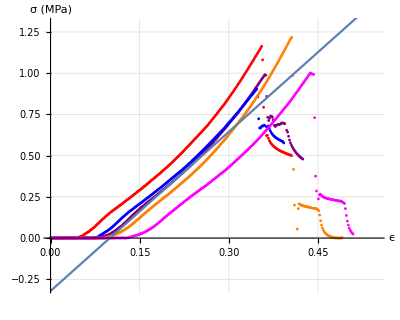

```mathematica
Show[ContourPlot[y==10,{x,.0,.55},{y,-.3,1.3},GridLines->Automatic,GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}],g1,g2,g3,g4,g5,Plot[line1,{x,0,.7},PlotStyle->{Thickness[.004]}],AspectRatio->.8,Axes->True,Frame->False,AxesLabel->{"ϵ","σ (MPa)"}]
```

### Parte 2 (Baterias de 6 a 10)

```mathematica
v2 = .8;
```

```mathematica
bat6=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt2\\BAT6.xls"];
d6=12.81;
h6=30.75;
fTAV6=Table[{bat6[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d6^2 (* A[mm^2]*),v2 (* v[mm/s] *)},{i,1,Length[bat6]}];
deltaSt6=Table[{fTAV6[[i]][[2]]fTAV6[[i]][[4]],fTAV6[[i]][[1]]/fTAV6[[i]][[3]]},{i,1,Length[bat6]}];
strainStress6=Table[{deltaSt6[[i]][[1]]/h6,deltaSt6[[i]][[2]]},{i,1,Length[bat6]}];
strainStressFit6=Table[{deltaSt6[[i]][[1]]/h6,deltaSt6[[i]][[2]]},{i,60,130}];
g6=ListPlot[strainStress6,PlotStyle->{Red,PointSize[.005]}];
```

```mathematica
bat7=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt2\\BAT7.xls"];
d7=12.89;
h7=31.78;
fTAV7=Table[{bat7[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d7^2 (* A[mm^2]*),v2 (* v[mm/s] *)},{i,1,Length[bat7]}];
deltaSt7=Table[{fTAV7[[i]][[2]]fTAV7[[i]][[4]],fTAV7[[i]][[1]]/fTAV7[[i]][[3]]},{i,1,Length[bat7]}];
strainStress7=Table[{deltaSt7[[i]][[1]]/h7,deltaSt7[[i]][[2]]},{i,1,Length[bat7]}];
strainStressFit7=Table[{deltaSt7[[i]][[1]]/h7,deltaSt7[[i]][[2]]},{i,60,130}];
g7=ListPlot[strainStress7,PlotStyle->{Magenta,PointSize[.005]}];
```

```mathematica
bat8=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt2\\BAT8.xls"];
d8=13.44;
h8=31.14;
fTAV8=Table[{bat8[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d8^2 (* A[mm^2]*),v2 (* v[mm/s] *)},{i,1,Length[bat8]}];
deltaSt8=Table[{fTAV8[[i]][[2]]fTAV8[[i]][[4]],fTAV8[[i]][[1]]/fTAV8[[i]][[3]]},{i,1,Length[bat8]}];
strainStress8=Table[{deltaSt8[[i]][[1]]/h8,deltaSt8[[i]][[2]]},{i,1,Length[bat8]}];
strainStressFit8=Table[{deltaSt8[[i]][[1]]/h8,deltaSt8[[i]][[2]]},{i,60,130}];
g8=ListPlot[strainStress8,PlotStyle->{Blue,PointSize[.005]}];
```

```mathematica
bat9=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt2\\BAT9.xls"];
d9=13.6;
h9=30.91;
fTAV9=Table[{bat9[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d9^2 (* A[mm^2]*),v2 (* v[mm/s] *)},{i,1,Length[bat9]}];
deltaSt9=Table[{fTAV9[[i]][[2]]fTAV9[[i]][[4]],fTAV9[[i]][[1]]/fTAV9[[i]][[3]]},{i,1,Length[bat9]}];
strainStress9=Table[{deltaSt9[[i]][[1]]/h9,deltaSt9[[i]][[2]]},{i,1,Length[bat9]}];
strainStressFit9=Table[{deltaSt9[[i]][[1]]/h9,deltaSt9[[i]][[2]]},{i,60,130}];
g9=ListPlot[strainStress9,PlotStyle->{Red,PointSize[.005]}];
```

```mathematica
bat10=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt2\\BAT10.xls"];
d10=13.52;
h10=31.03;
fTAV10=Table[{bat10[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d10^2 (* A[mm^2]*),v2 (* v[mm/s] *)},{i,1,Length[bat10]}];
deltaSt10=Table[{fTAV10[[i]][[2]]fTAV10[[i]][[4]],fTAV10[[i]][[1]]/fTAV10[[i]][[3]]},{i,1,Length[bat10]}];
strainStress10=Table[{deltaSt10[[i]][[1]]/h10,deltaSt10[[i]][[2]]},{i,1,Length[bat10]}];
strainStressFit10=Table[{deltaSt10[[i]][[1]]/h10,deltaSt10[[i]][[2]]},{i,60,130}];
g10=ListPlot[strainStress10,PlotStyle->{Green,PointSize[.005]}];
```

```mathematica
pointsSet2=Join[strainStressFit6,strainStressFit7,strainStressFit8,strainStressFit9,strainStressFit10];
line2=Fit[pointsSet2, {1,x},x] (* Daqui tiramos que E = 3.54 MPa*)
```

-0.370173+3.5426 x

```mathematica
dP2=StandardDeviation[pointsSet2]
```

{0.0528346,0.213888}

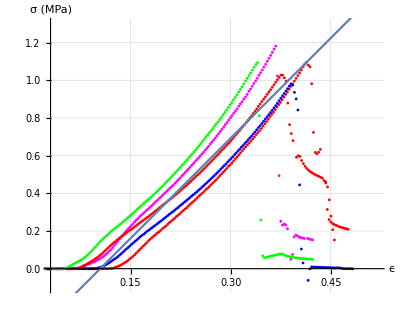

```mathematica
Show[ContourPlot[y==10,{x,.03,.52},{y,-.1,1.3},GridLines->Automatic,GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}],g6,g7,g8,g9,g10,Plot[line2,{x,-.3,.7},PlotStyle->{Thickness[.004]}],AspectRatio->.8,Axes->True,Frame->False,AxesLabel->{"ϵ","σ (MPa)"}]
```

### Parte 3 (Baterias de 11 a 15)

```mathematica
v3 = 1.2;
```

```mathematica
bat11=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt3\\BAT11.xls"];
d11=13.15;
h11=31.5;
fTAV11=Table[{bat11[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d11^2 (* A[mm^2]*),v3 (* v[mm/s] *)},{i,1,Length[bat11]}];
deltaSt11=Table[{fTAV11[[i]][[2]]fTAV11[[i]][[4]],fTAV11[[i]][[1]]/fTAV11[[i]][[3]]},{i,1,Length[bat11]}];
strainStress11=Table[{deltaSt11[[i]][[1]]/h11,deltaSt11[[i]][[2]]},{i,1,Length[bat11]}];
strainStressFit11=Table[{deltaSt11[[i]][[1]]/h11,deltaSt11[[i]][[2]]},{i,80,100}];
g11=ListPlot[strainStress11,PlotStyle->{Green,PointSize[.005]}];
```

```mathematica
bat12=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt3\\BAT12.xls"];
d12=13.15;
h12=31.5;
fTAV12=Table[{bat12[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d12^2 (* A[mm^2]*),v3(* v[mm/s] *)},{i,1,Length[bat12]}];
deltaSt12=Table[{fTAV12[[i]][[2]]fTAV12[[i]][[4]],fTAV12[[i]][[1]]/fTAV12[[i]][[3]]},{i,1,Length[bat12]}];
strainStress12=Table[{deltaSt12[[i]][[1]]/h12,deltaSt12[[i]][[2]]},{i,1,Length[bat12]}];
strainStressFit12=Table[{deltaSt12[[i]][[1]]/h12,deltaSt12[[i]][[2]]},{i,80,100}];
g12=ListPlot[strainStress12,PlotStyle->{Magenta,PointSize[.005]}];
```

```mathematica
bat13=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt3\\BAT13.xls"];
d13=13.53;
h13=30.71;
fTAV13=Table[{bat13[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d13^2 (* A[mm^2]*),v3 (* v[mm/s] *)},{i,1,Length[bat13]}];
deltaSt13=Table[{fTAV13[[i]][[2]]fTAV13[[i]][[4]],fTAV13[[i]][[1]]/fTAV13[[i]][[3]]},{i,1,Length[bat13]}];
strainStress13=Table[{deltaSt13[[i]][[1]]/h13,deltaSt13[[i]][[2]]},{i,1,Length[bat13]}];
strainStressFit13=Table[{deltaSt13[[i]][[1]]/h13,deltaSt13[[i]][[2]]},{i,80,100}];
g13=ListPlot[strainStress13,PlotStyle->{Orange,PointSize[.005]}];
```

```mathematica
bat14=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt3\\BAT14.xls"];
d14=13.32;
h14=30.71;
fTAV14=Table[{bat14[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d14^2 (* A[mm^2]*),v3 (* v[mm/s] *)},{i,1,Length[bat14]}];
deltaSt14=Table[{fTAV14[[i]][[2]]fTAV14[[i]][[4]],fTAV14[[i]][[1]]/fTAV14[[i]][[3]]},{i,1,Length[bat14]}];
strainStress14=Table[{deltaSt14[[i]][[1]]/h14,deltaSt14[[i]][[2]]},{i,1,Length[bat14]}];
strainStressFit14=Table[{deltaSt14[[i]][[1]]/h14,deltaSt14[[i]][[2]]},{i,80,100}];
g14=ListPlot[strainStress14,PlotStyle->{Blue,PointSize[.005]}];
```

```mathematica
bat15=Import["C:\\Users\\renan\\Desktop\\576\\stages\\xls\\pt3\\BAT15.xls"];
d15=13.28;
h15=32.51;
fTAV15=Table[{bat15[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d15^2 (* A[mm^2]*),v3 (* v[mm/s] *)},{i,1,Length[bat15]}];
deltaSt15=Table[{fTAV15[[i]][[2]]fTAV15[[i]][[4]],fTAV15[[i]][[1]]/fTAV15[[i]][[3]]},{i,1,Length[bat15]}];
strainStress15=Table[{deltaSt15[[i]][[1]]/h15,deltaSt15[[i]][[2]]},{i,1,Length[bat15]}];
strainStressFit15=Table[{deltaSt15[[i]][[1]]/h15,deltaSt15[[i]][[2]]},{i,80,100}];
g15=ListPlot[strainStress15,PlotStyle->{Red,PointSize[.005]}];
```

```mathematica
pointsSet3=Join[strainStressFit11,strainStressFit12,strainStressFit13,strainStressFit14,strainStressFit15];
line3=Fit[pointsSet3, {1,x},x] (* Daqui tiramos que E = 3.77 MPa*)
```

-0.852542+3.77474 x

```mathematica
dP3=StandardDeviation[pointsSet3]
```

{0.0243529,0.167873}

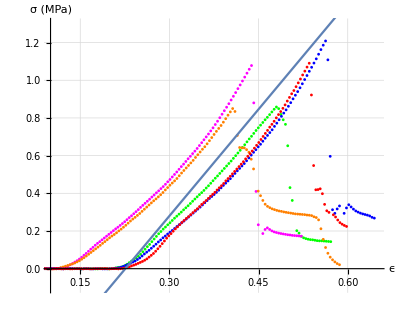

```mathematica
Show[ContourPlot[y==10,{x,.1,.65},{y,-.1,1.3},GridLines->Automatic,GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}],g11,g12,g13,g14,g15,Plot[line3,{x,-.3,.7},PlotStyle->{Thickness[.004]}],AspectRatio->.8,Axes->True,Frame->False,AxesLabel->{"ϵ","σ (MPa)"}]
```

### Correlacionando os módulos de elasticidade com a velocidade de deformação

```mathematica
vE={{v1,line1[[2,1]]},{v2,line2[[2,1]]},{v3,line3[[2,1]]}};
```

```mathematica
g =Simplify[InterpolatingPolynomial[vE,x]]
```

2.39383+2.00638 x-0.713018 x^2

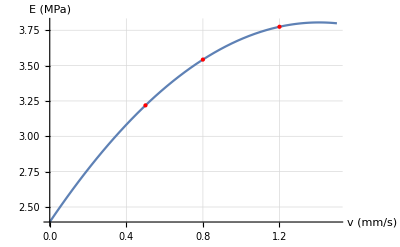

```mathematica
Show[Plot[g,{x,0,1.5},GridLines->Automatic,GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}},AxesLabel->{"v (mm/s)","E (MPa)"}],ListPlot[vE,PlotStyle->{Red,PointSize[Large]}]]
```

### Desvios

```mathematica
deviationList=TableForm[Join[{dP1},{dP2},{dP3}]]
```

0.04963 | 0.197507
0.0528346 | 0.213888
0.0243529 | 0.167873